```mathematica
Clear[k,i,j,b];
k=1;



neighborCount[k_,{i_,j_}]:=BooleanCountingFunction[{k},Delete[Flatten@Array[b,{3,3},{i,j}-1],5]
];
```

(b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&b[1+i,-1+j]&&!b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&b[1+i,j]&&!b[1+i,1+j])||(!b[-1+i,-1+j]&&!b[-1+i,j]&&!b[-1+i,1+j]&&!b[i,-1+j]&&!b[i,1+j]&&!b[1+i,-1+j]&&!b[1+i,j]&&b[1+i,1+j])

```mathematica
life44
```

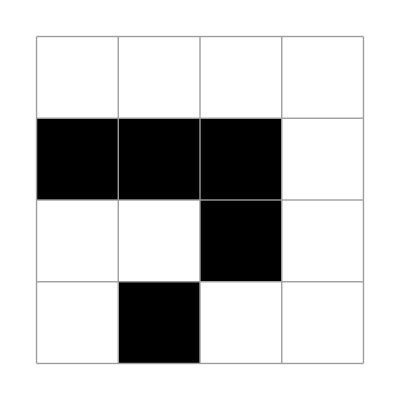
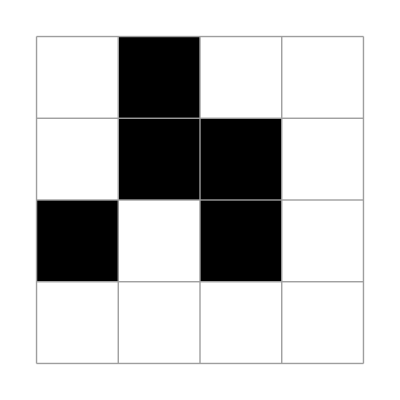
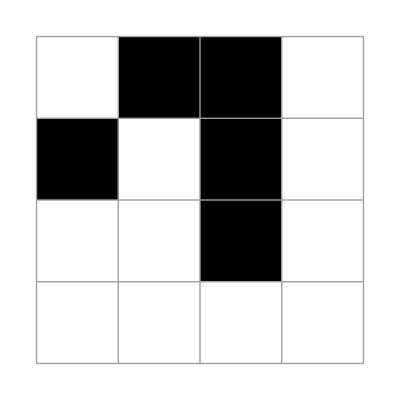
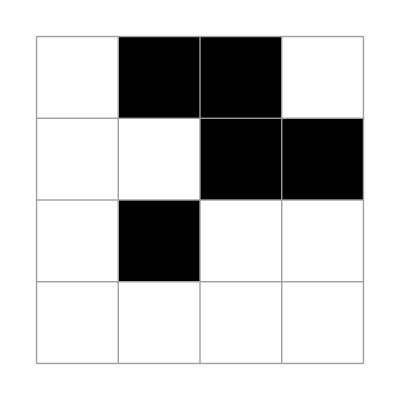

```mathematica
X1=({{0, 0, 0, 0}, {1, 1, 1, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}});
plt/@NestList[updateLife[{4,4}][ #]&,
X1,3]
```